```mathematica
(*Likelihood*)
sigmix=1;
L=MixtureDistribution[{1,1},{NormalDistribution[m1,sigmix],NormalDistribution[-m1,sigmix]}];lik[x_,m_]:=PDF[L,x]/.m1->m
```

```mathematica
Log[lik[10,mu]]//CForm
```

Log(1/(2.*Power(E,Power(10 - mu,2)/2.)*Sqrt(2*Pi)) + 
    1/(2.*Power(E,Power(10 + mu,2)/2.)*Sqrt(2*Pi)))

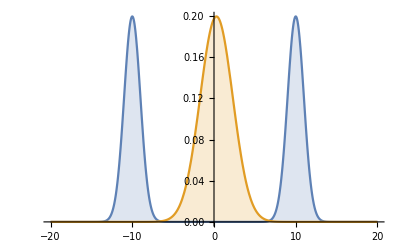

```mathematica
Data=10;
muhyp=0.3;
sighyp=2;
Plot[{lik[Data,μ],PDF[NormalDistribution[muhyp,sighyp],μ]},{μ,-20,20},Filling->Axis, PlotRange->All]
```

```mathematica
Data=10;
muhyp=0.3;
sighyp=2;
lik[Data,μ]PDF[NormalDistribution[muhyp,sighyp],μ]//FullSimplify
```

ⅇ^((-9.925-0.625 μ) μ) (7.5884×10^-24+7.5884×10^-24 ⅇ^(20. μ))

```mathematica
∫lik[Data,μ]PDF[NormalDistribution[muhyp,sighyp],μ]ⅆμ
```

3.65669×10^-6 Erf[0.632456 (-10.075+1.25 μ)]+1.10137×10^-6 Erf[0.632456 (9.925+1.25 μ)]

```mathematica
Z=∫_(-∞)^∞ lik[Data,μ]PDF[NormalDistribution[muhyp,sighyp],μ]ⅆμ//N//Re
```

9.51613×10^-6

```mathematica
Log[Z]
```

-11.5625

```mathematica
post[mu_]:=(lik[Data,mu]PDF[NormalDistribution[muhyp,sighyp],mu])/Z
```

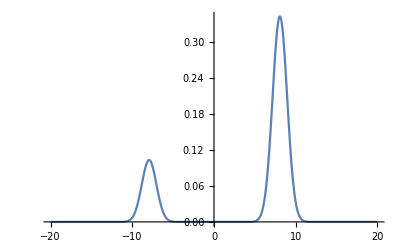

```mathematica
Plot[post[μ],{μ,-20,20},PlotRange->All]
```